# PROBLEM 01

{-5 ⅇ^(-Sin[x]),-4 ⅇ^(-Sin[x]),-3 ⅇ^(-Sin[x]),-2 ⅇ^(-Sin[x]),-ⅇ^(-Sin[x]),0,ⅇ^(-Sin[x]),2 ⅇ^(-Sin[x]),3 ⅇ^(-Sin[x]),4 ⅇ^(-Sin[x]),5 ⅇ^(-Sin[x])}

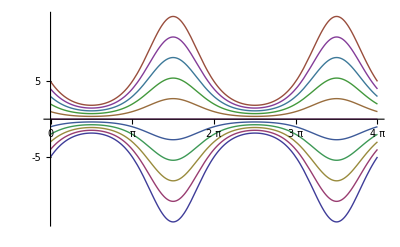

```mathematica
sol=DSolve[y'[x]==-Cos[x]*y[x],y[x],x];
tab=Table[y[x]/.sol[[1]]/.{C[1]->k},{k,-5,5,1}]
Plot[Evaluate[tab],{x,0,4*π},Ticks->{{0,π,2*π,3*π,4*π},{-5,5}}]
```

# PROBLEM 02

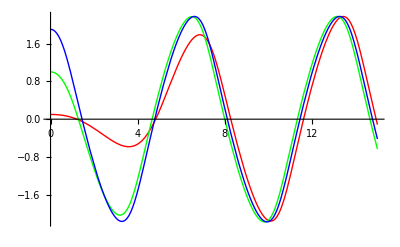

```mathematica
A1=NDSolve[{x''[t]+((1/3)*x'[t]^2-1)*x'[t]+x[t]==0,x[0]==0.1,x'[0]==0},x[t],{t,0,15}];
B1=NDSolve[{x''[t]+((1/3)*x'[t]^2-1)*x'[t]+x[t]==0,x[0]==1.0,x'[0]==0},x[t],{t,0,15}];
C1=NDSolve[{x''[t]+((1/3)*x'[t]^2-1)*x'[t]+x[t]==0,x[0]==1.9,x'[0]==0},x[t],{t,0,15}];
Plot[Evaluate[x[t]/.{A1,B1,C1}],{t,0,15},PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1]}]
```

# PROBLEM 03

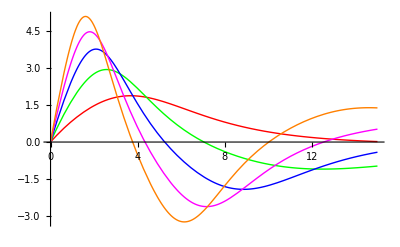

```mathematica
T1=NDSolve[{x''[t]+0.3*x'[t]+0.04*x[t]^3==0,x[0]==0,x'[0]==1},x[t],{t,0,15}];
T2=NDSolve[{x''[t]+0.3*x'[t]+0.04*x[t]^3==0,x[0]==0,x'[0]==2},x[t],{t,0,15}];
T3=NDSolve[{x''[t]+0.3*x'[t]+0.04*x[t]^3==0,x[0]==0,x'[0]==3},x[t],{t,0,15}];
T4=NDSolve[{x''[t]+0.3*x'[t]+0.04*x[t]^3==0,x[0]==0,x'[0]==4},x[t],{t,0,15}];
T5=NDSolve[{x''[t]+0.3*x'[t]+0.04*x[t]^3==0,x[0]==0,x'[0]==5},x[t],{t,0,15}];
Plot[Evaluate[x[t]/.{T1,T2,T3,T4,T5}],{t,0,15},PlotStyle->{Red,Green,Blue,Magenta,Orange}]
```

# PROBLEM 04

```mathematica
Eq={x'[t]==σ (y[t]-x[t]),y'[t]==x[t] (ρ-z[t])-y[t],z'[t]==x[t] y[t]-β z[t]};
init={x[0]==10,y[0]==10,z[0]==10};
pars={σ->10,ρ->28,β->8/3};
{x1,y1,z1}=NDSolveValue[{Eq/.pars,init},{x[t],y[t],z[t]},{t,0,50}];
ParametricPlot3D[{x1,y1,z1},{t,0,50}]
```

-Graphics3D-

# PROBLEM 05

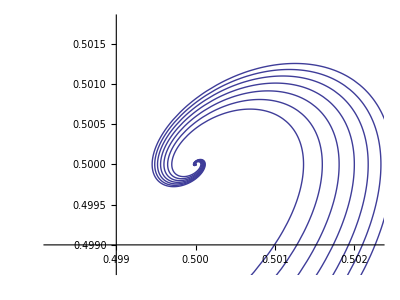

```mathematica
Eq={x'[t]==x [t]*(α-β*y[t]),y'[t]==y[t] (δ*x[t]-y[t])};
pars={α->2/3,β->4/3,γ->1,δ->1};
k=.9;
Do[
init={x[0]==k,y[0]==k};
{x[i],y[i]}=NDSolveValue[{Eq/.pars,init},{x[t],y[t]},{t,0,50}];
k=k+.1;
,{i,1,7}]
g1=ParametricPlot[{x[1],y[1]},{t,10,50}];
g2=ParametricPlot[{x[2],y[2]},{t,10,50}];
g3=ParametricPlot[{x[3],y[3]},{t,10,50}];
g4=ParametricPlot[{x[4],y[4]},{t,10,50}];
g5=ParametricPlot[{x[5],y[5]},{t,10,50}];
g6=ParametricPlot[{x[6],y[6]},{t,10,50}];
g7=ParametricPlot[{x[7],y[7]},{t,10,50}];
Show[g1,g2,g3,g4,g5,g6,g7]
```

# PROBLEM 06

```mathematica
eq=D[u[x,y],{x,2}]+D[u[x,y],{y,2}]==0;
```

```mathematica
DSolve[LaplaceEquation,u[x,y],{x,y}]
```

{{u[x,y]→C[1][ⅈ x+y]+C[2][-ⅈ x+y]}}

```mathematica
DSolve[{b *D[y[x,t],t]+a *D[y[x,t],x]==c *Sin[x],y[0,t]==a *Cos[t]},y[x,t],{x,t}]
```